```mathematica
x = RandomVariate[NormalDistribution[0,1],{2,3}]
```

{{-0.428046,0.984672,1.04767},{1.26332,1.45965,0.464724}}

```mathematica
wish = RandomVariate[NormalDistribution[0,1],{1000,10000}]
```

{{-1.9402,-2.11455,-0.399956,0.486184,-0.622795,0.0892778,9988,-0.441295,-0.740011,-0.689165,0.41218,-1.24322,0.0696442},998,{1}}
 |  |  |  |

```mathematica
Dimensions[wish]
```

{1000,10000}

```mathematica
woe = wish.Transpose[wish]
```

{1}
 |  |  |  |

```mathematica
EVALS =Sort[Eigenvalues[woe]];
```

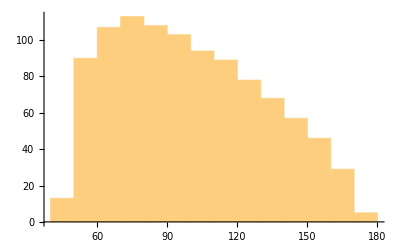

```mathematica
Histogram[EVALS / Sqrt[10000]]
```

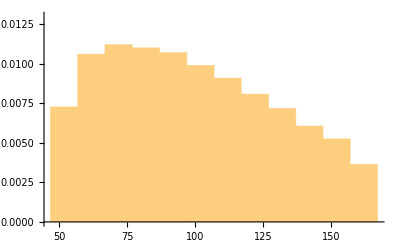

```mathematica
Show[
Histogram[EVALS / Sqrt[10000],{Min[EVALS / Sqrt[10000]],Max[EVALS / Sqrt[10000]],Automatic},PDF],
Plot[PDF[MarchenkoPasturDistribution[1/2],x],{x,0,4},PlotStyle->Thick,Exclusions->None,PlotRange->{0,0.013}]]
```